### Prima

```mathematica
Clear["*"]
```

```mathematica
fun=∏_(i=1)^t (i/T)
```

(1/T)^t Gamma[1+t]

```mathematica
T=20;
```

```mathematica
fun
```

20^-t Gamma[1+t]

```mathematica
Nu=1024;dt=1;
```

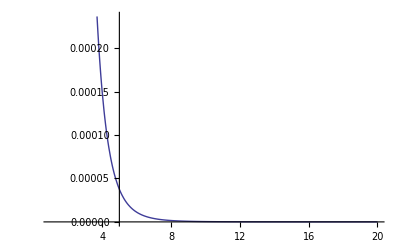

```mathematica
Plot[fun,{t,1,T}]
```

```mathematica
FourierTransform[fun,t,ω,FourierParameters->{0,-2Pi}]
```

FourierTransform[20^-t Gamma[1+t],t,ω,FourierParameters→{0,-2 π}]

#### Numerical

```mathematica
tempi=N[Table[t,{t,1,T,(T-1)/1023}]];
```

```mathematica
Length[tempi]
```

1024

```mathematica
data=N[Table[fun,{t,1,T,(T-1)/1023}]];
```

```mathematica
Length[data]
```

1024

```mathematica
frequencies=Range[-Nu/2,Nu/2-1];
```

```mathematica
Length[frequencies]
```

1024

```mathematica
transf=Fourier[data];
```

```mathematica
res={frequencies,transf};
```

```mathematica
res=Transpose[res];
```

```mathematica
Dimensions[res]
```

{1024,2}

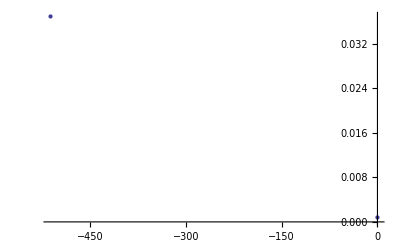

```mathematica
ListPlot[res]
```

### Seconda

```mathematica
Clear["*"]
```

```mathematica
fun2=Cos[2π f0(t-T/2)]*∏_(i=1)^t ((i-T/2)/T)
```

T^-t Cos[2 f0 π (t-T/2)] Pochhammer[1-T/2,t]

```mathematica
f0=280;T=20;
```

```mathematica
fun2
```

20^-t Cos[560 π (-10+t)] Pochhammer[-9,t]

```mathematica
Nu=4096;dt=1/6;
```

Plot[ ∏_(i=1)^t ((i-T/2)/T) ,{t,1,T},PlotPoints→(T/dt),PlotRange→Full]

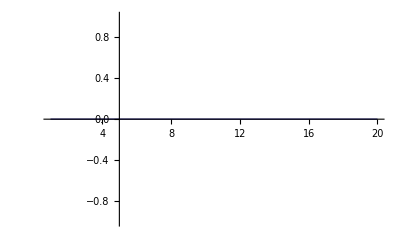

```mathematica
Plot[fun2,{t,1,T},PlotPoints->(T/dt),PlotRange->Full]
```

```mathematica
FourierTransform[fun2,t,ω,FourierParameters->{0,-2Pi}]
```

$Aborted